## Classes 5

Лабораторная работа №5.  Численные расчеты в системе Mathematica

#### Задание 1

а) Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

б) Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3                5
```

15

```mathematica
2+        7
```

9

```mathematica
2/3
```

2/3

в) Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
17^(1/2)
```

√17

```mathematica
3      /7
```

3/7

г) Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
17.          ^(1/2)
```

4.12311

```mathematica
4.123105625617661
```

д) Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
3 6+5
```

23

```mathematica
3(6 +  5 )
```

33

#### Задание 2

а) С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17], 200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

б) Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа.

```mathematica
N[ⅇ^(π *Sqrt[163]), 40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[%]
```

262537412640768744

в) Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

г) Последовательно введите выражение

```mathematica
5>3
5<2
```

True

False

Справедливо ли неравенство

```mathematica
π^ⅇ>ⅇ^π
```

False

```mathematica
N[π^ⅇ, 10]
N[ⅇ^π, 10]
```

22.45915772

23.14069263

#### Задание 3

а) Решить уравнения

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

б) Решить системы уравнений

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

в) Придумать свою

```mathematica
NSolve[{(4 x^2+y^3+4 y)/(y^3-4y)==4, x^2 y+y^2 x== 48}, {x,y}]
```

{{x→-3.11081-2.64394 ⅈ,y→-0.187033-2.043 ⅈ},{x→-3.11081+2.64394 ⅈ,y→-0.187033+2.043 ⅈ},{x→2.66518,y→3.11554},{x→2.89968-4.1189 ⅈ,y→0.441624+2.54059 ⅈ},{x→2.89968+4.1189 ⅈ,y→0.441624-2.54059 ⅈ},{x→1.26886-3.22893 ⅈ,y→-3.2854-0.427919 ⅈ},{x→1.26886+3.22893 ⅈ,y→-3.2854+0.427919 ⅈ},{x→-6.11398,y→4.27941}}

#### Задание 4

Вариант 16

```mathematica
FindRoot[2 Cos[x]==Exp[-2  x], {x,-1,2}]
```

{x→1.54819}

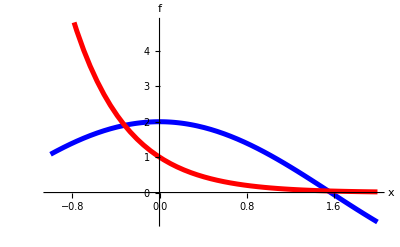

```mathematica
Plot[{2 Cos[x],Exp[-2  x]}, {x,-1,2},
PlotStyle->{{Thickness[0.009], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}, AxesLabel->{"x", "f"}]
```

```mathematica
FindRoot[2 Cos[x]==Exp[-2  x], {x, -0.35}]
```

{x→-0.32045}

```mathematica
FindRoot[2 Cos[x]==Exp[-2  x], {x, 1.55}]
```

{x→1.54819}

#### Задание 5

```mathematica
sol1=NDSolve[{y''[x]+2  y'[x] ArcTan[x]+3 y[x]==0, y[0]==-1, y'[0]==2},y, {x,-3,2}]
```

{{y→InterpolatingFunction[…]}}

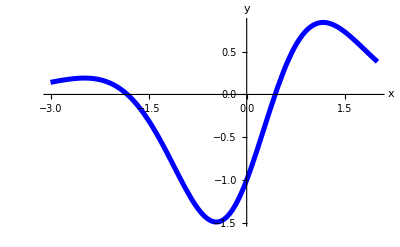

```mathematica
Plot[y[x]/.sol1, {x,-3,2}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
sol2=FindRoot[(y[x]/.sol1[[1]])==0, {x,-1.8}]
```

{x→-1.82634}

```mathematica
sol22=FindRoot[(y[x]/.sol1[[1]])==0, {x,0.4}]
```

{x→0.435218}

```mathematica
D[y[x]/.sol1[[1]],x]/.sol2
```

-0.687278

```mathematica
D[y[x]/.sol1[[1]],x]/.sol22
```

2.23422

```mathematica
sol3=FindRoot[D[y[x]/.sol1[[1]],x]==0, {x,-0.5}]
```

{x→-0.464911}

```mathematica
y[x]/.sol1[[1]]/.sol3
```

-1.49166

```mathematica
FindMinimum[y[x]/.sol1[[1]], {x,-0.5}]
```

{-1.49166,{x→-0.464911}}

#### Задание 6 Примеры 2, 3

```mathematica
task2 = Table[{x,(21+42x+84Sin[x]+35Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,56.7108},{0.25,94.109},{0.5,106.705},{0.75,129.182},{1.,159.321},{1.25,153.083},{1.5,181.598},{1.75,166.755},{2.,161.527},{2.25,168.582},{2.5,140.929},{2.75,134.965},{3.,123.929},{3.25,108.744},{3.5,107.669},{3.75,110.833},{4.,109.773},{4.25,114.658},{4.5,110.689},{4.75,139.261},{5.,156.29}}

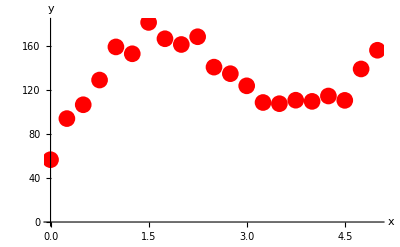

```mathematica
task2Plot=ListPlot[task2, PlotStyle->{ Red,PointSize[0.03]}, AxesLabel->{"x", "y"}]
```

```mathematica
y1=Fit[task2, {1,x,Cos[x], Sin[x]},x]
```

26.9318+39.6484 x+31.8408 Cos[x]+79.8247 Sin[x]

```mathematica
y2=Fit[task2, {1,x,x^2, x^3, x^4},x]
```

53.8095+155.397 x-61.5194 x^2+4.54512 x^3+0.478272 x^4

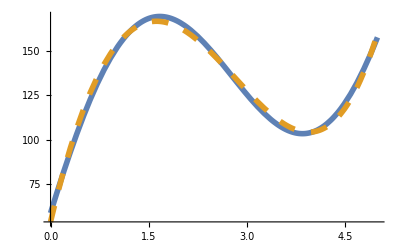

```mathematica
plot2 =Plot[{y1,y2}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

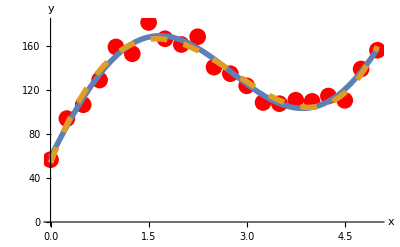

```mathematica
Show[task2Plot, plot2]
```

```mathematica
task3 = Table[{x,(21+42x+84Sin[x]+35Cos[2x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,5,0.25}]
```

{{0.,61.3439},{0.25,85.4774},{0.5,92.0354},{0.75,119.171},{1.,107.635},{1.25,123.358},{1.5,140.501},{1.75,132.5},{2.,169.851},{2.25,176.764},{2.5,182.408},{2.75,202.921},{3.,175.23},{3.25,176.785},{3.5,179.56},{3.75,135.726},{4.,126.758},{4.25,108.427},{4.5,105.569},{4.75,99.7503},{5.,133.025}}

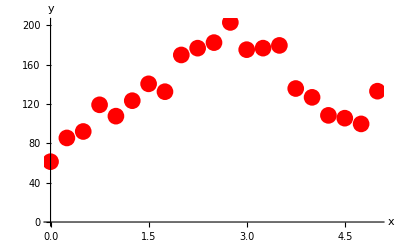

```mathematica
task3Plot=ListPlot[task3, PlotStyle->{ Red,PointSize[0.03]}, AxesLabel->{"x", "y"}]
```

```mathematica
y11=Fit[task3, {1,x,Cos[2x], Sin[x]},x]
```

24.1609+41.344 x+32.6652 Cos[2 x]+79.7251 Sin[x]

```mathematica
y22=Fit[task3, {1,x,x^2, x^3, x^4},x]
```

78.0549-28.3827 x+93.044 x^2-34.7059 x^3+3.51073 x^4

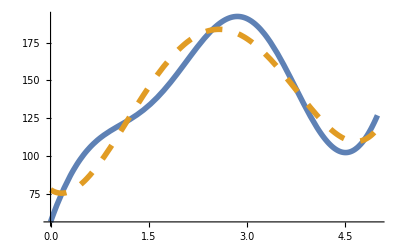

```mathematica
plot22 =Plot[{y11,y22}, {x,0,5},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

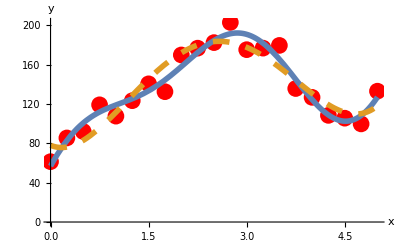

```mathematica
Show[task3Plot, plot22]
```